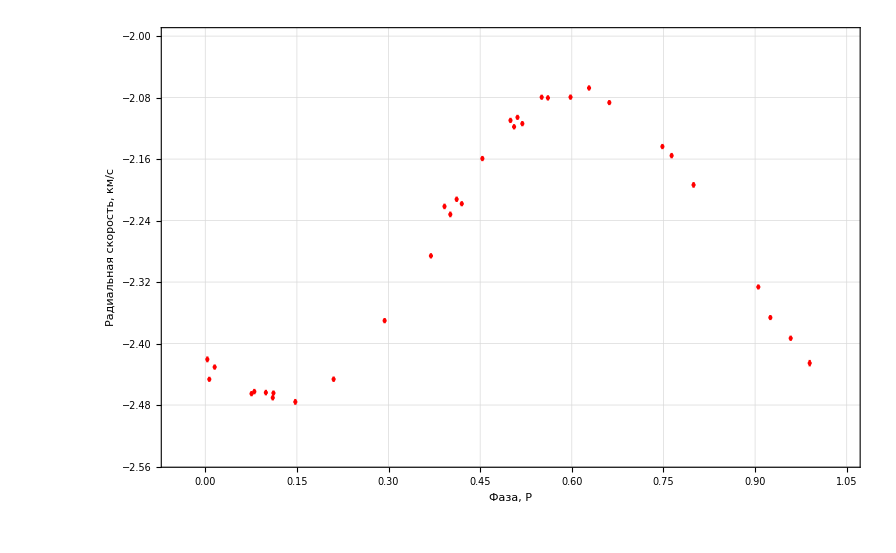

```mathematica
Clear["Global`*"]
SetDirectory["/Users/haykh/Dropbox/Documents/Sci_pop/Exoplanets"];
dataRaw=Import["velocity_data.dat"];
Needs["ErrorBarPlots`"]
data=Table[{{dataRaw⟦i,1⟧,dataRaw⟦i,2⟧},ErrorBar[dataRaw⟦i,3⟧]},{i,Length[dataRaw]}];
ErrorListPlot[data,
PlotStyle->Directive[PointSize[Small],Red],
Frame->True,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->{{-0.05,1.05},{-2.55,-2.}},
FrameTicksStyle->Directive[15,Gray],
FrameLabel->{"Фаза, P","Радиальная скорость, км/с"},
LabelStyle->Directive[15,Black]
]
```

```mathematica
dataRaw
```

dataRaw